```mathematica
ω[z_,c_]:=z+c⟦1⟧/z+ c⟦2⟧/z^2+ c⟦3⟧/z^3+ c⟦4⟧/z^4+ c⟦5⟧/z^5+ c⟦6⟧/z^6+ c⟦7⟧/z^7;
dω[z_,c_]:=1-c⟦1⟧/z^2-2 c⟦2⟧/z^3-3 c⟦3⟧/z^4-4 c⟦4⟧/z^5-5 c⟦5⟧/z^6-6 c⟦6⟧/z^7-7 c⟦7⟧/z^8;
φ0[z_,a_]:=a⟦1⟧/z+a⟦2⟧/z^2+a⟦3⟧/z^3+a⟦4⟧/z^4+a⟦5⟧/z^5+a⟦6⟧/z^6+a⟦7⟧/z^7;
dφ0[z_,a_]:=-a⟦1⟧/z^2-2 a⟦2⟧/z^3-3 a⟦3⟧/z^4-4 a⟦4⟧/z^5-5 a⟦5⟧/z^6-6 a⟦6⟧/z^7-7 a⟦7⟧/z^8;
ϕ0[z_,a_,c_]:=dφ0[z,a]/dω[z,c];
ϕ[z_,a_,c_]:=(1/4+dφ0[z,a])/dω[z,c];
Q[z_,q_]:=q⟦1⟧+q⟦2⟧ z+q⟦3⟧ z^2+q⟦4⟧ z^3+q⟦5⟧ z^4+q⟦6⟧ z^5+q⟦7⟧ z^6+q⟦8⟧ z^7;
Kk[z_,k_]:=Conjugate[k⟦1⟧]/z+Conjugate[k⟦2⟧]/z^2+Conjugate[k⟦3⟧]/z^3;
ψ0[z_,a_,c_,q_,k_]:=-1/(4 z)-Conjugate[Q[z,q]]ϕ[z,a,c]-Kk[z,k]; 

sω[z_]:=1/z-1/6 z^3+1/56 z^7;
sφ[z_]:=0.25/z+0.426 z+0.046 z^3+0.008 z^5-0.004 z^7;
sψ[z_]:=-(0.5/z+(0.548 z -0.457 z^3-0.026 z^5-0.029 z^7)/(1+0.5 z^4-0.125 z^8));
```

```mathematica
c={0,0,-0.166667,0,0,0,0.0178571};
p={0,0,-0.175595,0,0,0,0.0178571};
q={0,1.09003,0,0,0,-0.0219494,0,0};
a={0.425894,0,0.0463836,0,0.00760525,0,-0.00446429} ; 
k={0.0249923,0,0.00667723,0,-0.00548735,0,0};

c//N
p//N
q//N
a//N
k//N

Γ1=1/4;
Γ2=-1/2;

φ[z_,c_,a_]:=Γ1 z+φ0[z,a];
ψ[z_,a_,c_,q_,k_]:=Γ2 z+ψ0[z,a,c,q,k];

(* function derivation *)
```

{0.,0.,-0.166667,0.,0.,0.,0.0178571}

{0.,0.,-0.175595,0.,0.,0.,0.0178571}

{0.,1.09003,0.,0.,0.,-0.0219494,0.,0.}

{0.425894,0.,0.0463836,0.,0.00760525,0.,-0.00446429}

{0.0249923,0.,0.00667723,0.,-0.00548735,0.,0.}

```mathematica
S=1000;
aa=Table[N[i/S*π/2],{i,0,S}];
rr=1.1;
```

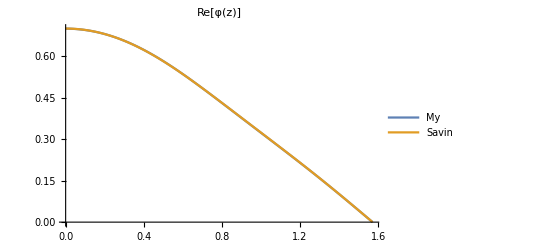

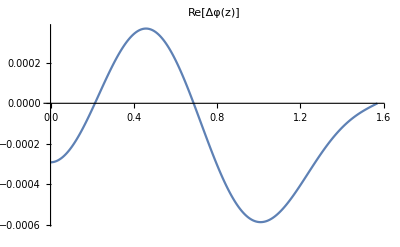

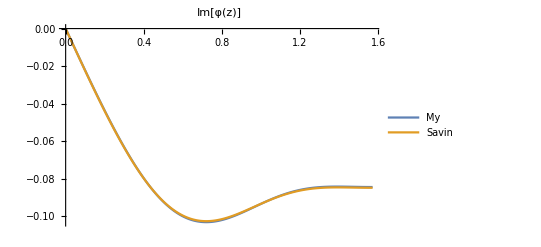

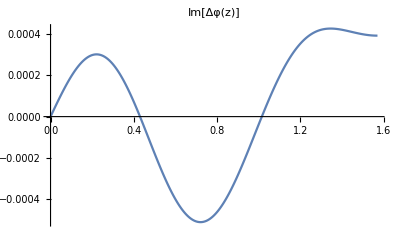

```mathematica
mPhi=φ[z,c,a];
sPhi=sφ[z];

sMyPhiData={#,Re[mPhi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPhiData={#,Re[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPhiData,sSavinPhiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[φ(z)]"]
deltaPhiData={#,Re[mPhi/.z->rr*Exp[ⅈ #]]-Re[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPhiData,Joined->True,PlotLabel->"Re[Δφ(z)]"]

sMyPhiData={#,Im[mPhi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPhiData={#,Im[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPhiData,sSavinPhiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[φ(z)]"]
deltaPhiData={#,Im[mPhi/.z->rr*Exp[ⅈ #]]-Im[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPhiData,Joined->True,PlotLabel->"Im[Δφ(z)]"]
```

(0.000834652+0.000519756 z^2+0.100356 z^4+0.0132503 z^6+0.204707 z^8-0.545826 z^10-0.5 z^12)/(z^3 (-0.125+0.500001 z^4+z^8))

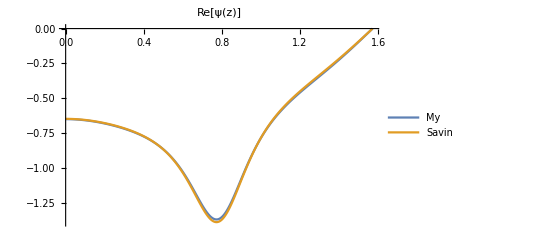

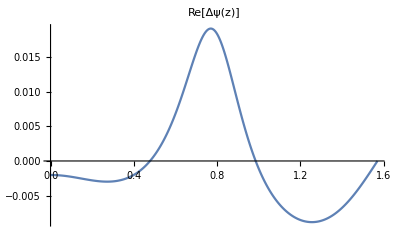

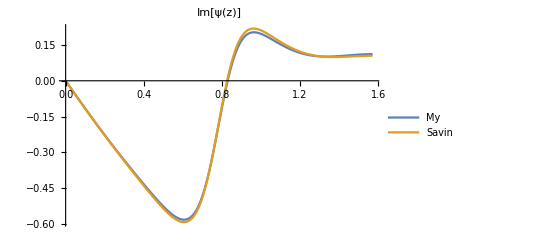

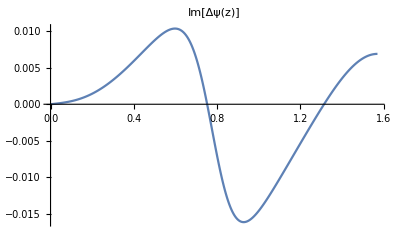

```mathematica
psi=Γ2*z-Γ1/z-ϕ[z,a,c]*u[z] -Kk[z,k];
mPsi=psi/.u[z]->13/12*1/z//Simplify
sPsi=sψ[z];

sMyPsiData={#,Re[mPsi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Re[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsiData,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[ψ(z)]"]
deltaPsiData={#,Re[mPsi/.z->rr*Exp[ⅈ #]]-Re[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPsiData,Joined->True,PlotLabel->"Re[Δψ(z)]"]

sMyPsiData={#,Im[mPsi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Im[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsiData,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[ψ(z)]"]
deltaPsiData={#,Im[mPsi/.z->rr*Exp[ⅈ #]]-Im[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPsiData,Joined->True,PlotLabel->"Im[Δψ(z)]"]
```

(-3.46945×10^-18+0.00950654 z^2+0.00707505 z^4+0.357446 z^6-0.5 z^8-0.197737 z^10+1.0566 z^12+0.851788 z^14)/(z (-0.125+0.500001 z^4+z^8)^2)

(-0.0219494+1.09003 z^4)/z^5

(0.109747-1.09003 z^4)/z^6

-1/2+0.0200317/z^4+0.274992/z^2-(0.25 (0.125-0.152105 z^2-0.556603 z^4-1.70358 z^6+z^8) du[z])/(-0.125+0.500001 z^4+z^8)-(0.851788 (-4.07313×10^-18+0.0111607 z^2+0.00830611 z^4+0.419642 z^6-0.587 z^8-0.232144 z^10+1.24045 z^12+1. z^14) u[z])/(z (-0.125+0.500001 z^4+z^8)^2)

1/(z^6 (-0.125+0.500001 z^4+z^8)^2)(0.000428699-6.09343×10^-10 z^2-0.00342962 z^4-0.0114078 z^6-0.00943349 z^8-0.266619 z^10+0.493921 z^12+0.0274386 z^14-0.919599 z^16-1.87268 z^18+0.5475 z^20-0.5 z^22)

direkt ψ

-((1/4+0.03125/z^8-0.0380263/z^6-0.139151/z^4-0.425894/z^2) (-0.0219494/z^5+1.09003/z))/(1-0.125/z^8+0.500001/z^4)-0.00667723/z^3-0.274992/z-z/2

direkt ψ'

1/(z^6 (-0.125+0.500001 z^4+z^8)^2)(0.000428699-6.09343×10^-10 z^2-0.00342962 z^4-0.0114078 z^6-0.00943349 z^8-0.266619 z^10+0.493921 z^12+0.0274386 z^14-0.919599 z^16-1.87268 z^18+0.5475 z^20-0.5 z^22)

1/(z^6 (-0.125+0.500001 z^4+z^8)^2)(0.000428699-6.09343×10^-10 z^2-0.00342962 z^4-0.0114078 z^6-0.00943349 z^8-0.266619 z^10+0.493921 z^12+0.0274386 z^14-0.919599 z^16-1.87268 z^18+0.5475 z^20-0.5 z^22)

1/(z^6 (-0.125+0.500001 z^4+z^8)^2)(0.000428699-6.09343×10^-10 z^2-0.00342962 z^4-0.0114078 z^6-0.00943349 z^8-0.266619 z^10+0.493921 z^12+0.0274386 z^14-0.919599 z^16-1.87268 z^18+0.5475 z^20-0.5 z^22)

(32.-35.072 z^2+119.744 z^4+60.928 z^6-1.632 z^8-29.856 z^10+17.064 z^12+0.624 z^14+0.732 z^16)/(z^2 (8.+4. z^4-1. z^8)^2)

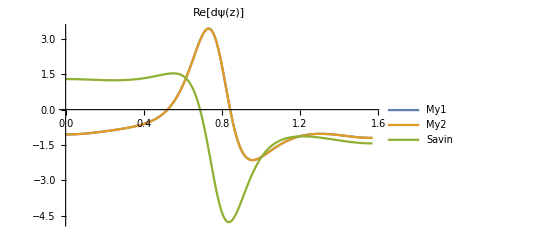

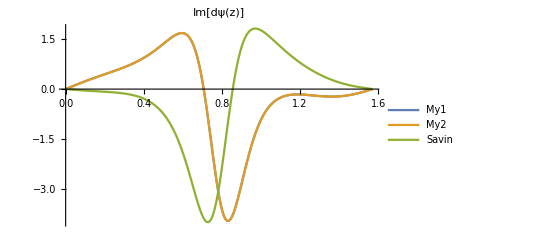

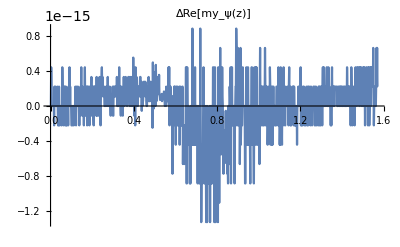

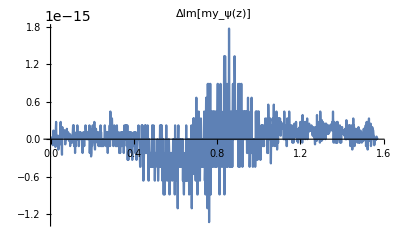

```mathematica
pphi=ϕ[z,a,c];
Dpphi=D[pphi,z]//Simplify
qq=Q[z,q]/.z->1/z//Simplify
dqq=(D[Q[z,q],z]/.z->1/z)*(-1/z^2)//Simplify
dpsi=Γ2+Γ1/z^2-Dpphi*u[z]-pphi*du[z] -D[Kk[z,k],z];
dpsi//Simplify
dpsi1=dpsi/.{u[z]->qq,du[z]->dqq}//Simplify

Print["direkt ψ"];
tpsi=psi/.u[z]->q⟦1⟧+Sum[q⟦k+1⟧/z^k,{k,1,7}]
Print["direkt ψ'"];
dpsi2=D[tpsi,z]//Simplify
mDPsi1=dpsi1
mDPsi2=dpsi2


sDPsi=D[sPsi,z]//Simplify

sMyPsi1Data={#,Re[mDPsi1/.z->rr*Exp[ⅈ #]]}&/@aa;
sMyPsi2Data={#,Re[mDPsi2/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Re[sDPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsi1Data,sMyPsi2Data,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My1","My2","Savin"}],PlotLabel->"Re[dψ(z)]",PlotRange->All]

sMyPsi1Data={#,Im[mDPsi1/.z->rr*Exp[ⅈ #]]}&/@aa;
sMyPsi2Data={#,Im[mDPsi2/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Im[sDPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsi1Data,sMyPsi2Data,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My1","My2","Savin"}],PlotLabel->"Im[dψ(z)]",PlotRange->All]

ListPlot[{#,Re[(mDPsi1-mDPsi2)/.z->rr*Exp[ⅈ #]]}&/@aa,Joined->True,PlotLabel->"ΔRe[my_ψ(z)]",PlotRange->All]
ListPlot[{#,Im[(mDPsi1-mDPsi2)/.z->rr*Exp[ⅈ #]]}&/@aa,Joined->True,PlotLabel->"ΔIm[my_ψ(z)]",PlotRange->All]
```

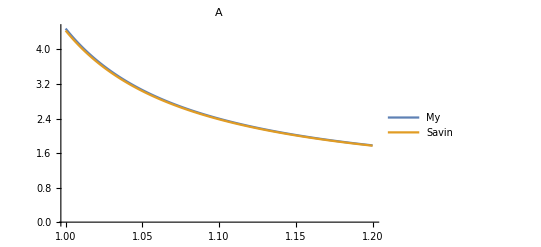

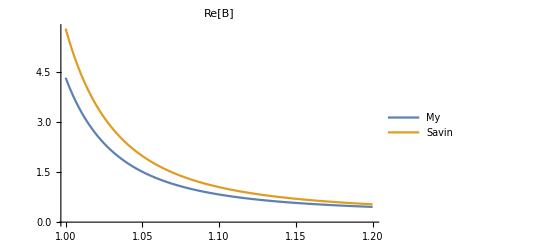

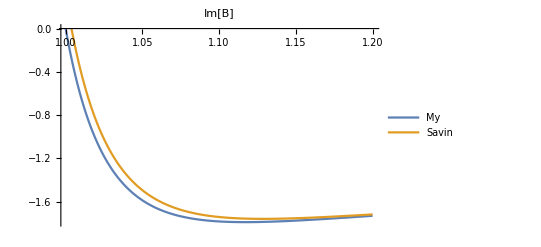

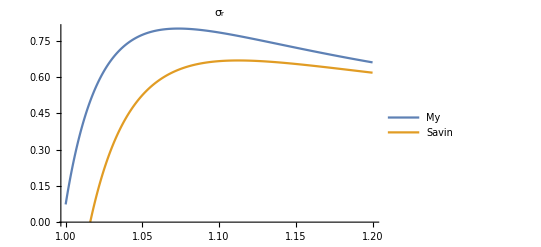

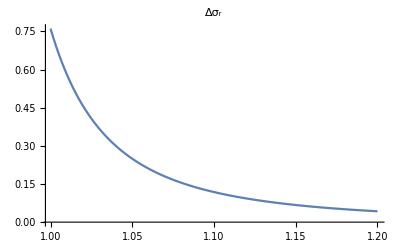

σ_φ(0)=4.41112

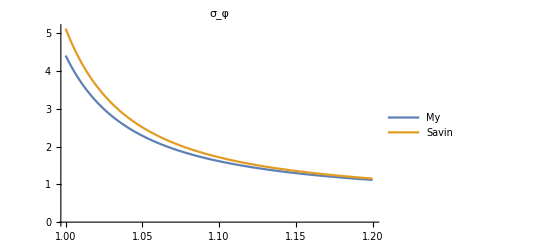

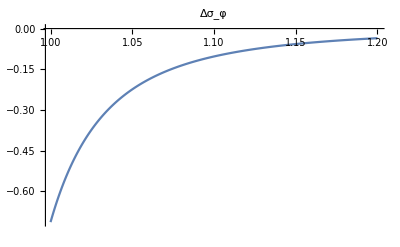

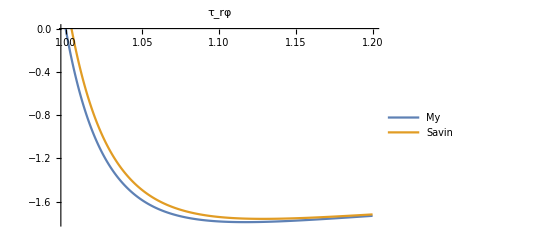

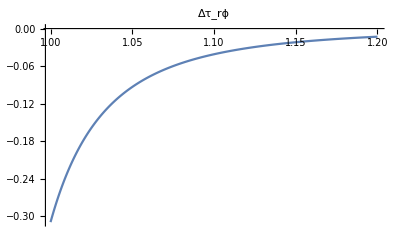

```mathematica
S=1000;
ρ=Table[N[(1+0.2*i/S)*Exp[ⅈ π/4]],{i,0,S}];
w=ω[z,c];
dw=D[w,z];
ddw=D[dw,z];

sw=sω[z];
dsw=D[sw,z];
ddsw=D[dsw,z];
spphi=D[sPhi,z]/dsw;
Dspphi=D[spphi,z];

A=4*Re[pphi]/.z->#&/@ρ;
B=2*z^2/(Abs[z]^2*Conjugate[dw])*(Conjugate[w]*Dpphi+mDPsi1)/.z->#&/@ρ;

sA=4*Re[spphi]/.z->1/#&/@ρ;
sB=2*z^2/(Abs[z]^2*Conjugate[dsw])*(Conjugate[sw]*Dspphi+sDPsi)/.z->1/#&/@ρ;

σr=(A-Re[B])/2;
σf=(A+Re[B])/2;
τ=Im[B];

sσr=(sA-Re[sB])/2;
sσf=(sA+Re[sB])/2;
sτ=Im[sB];

ρ=Abs[ρ];

ListPlot[{Transpose[{ρ,A}],Transpose[{ρ,sA}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"A"]
ListPlot[{Transpose[{ρ,Re[B]}],Transpose[{ρ,Re[sB]}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[B]",PlotRange->All]
ListPlot[{Transpose[{ρ,Im[B]}],Transpose[{ρ,Im[sB]}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[B]",PlotRange->Automatic]


ListPlot[{Transpose[{ρ,σr}],Transpose[{ρ,sσr}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"σ_r"]
ListPlot[Transpose[{ρ,σr-sσr}],Joined->True,PlotLabel->"Δσ_r",PlotRange->All]
Print["σ_φ(0)=",σf⟦1⟧];
ListPlot[{Transpose[{ρ,σf}],Transpose[{ρ,sσf}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"σ_φ"]
ListPlot[Transpose[{ρ,σf-sσf}],Joined->True,PlotLabel->"Δσ_φ",PlotRange->All]
ListPlot[{Transpose[{ρ,τ}],Transpose[{ρ,sτ}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"τ_rφ"]
ListPlot[Transpose[{ρ,τ-sτ}],Joined->True,PlotLabel->"Δτ_rϕ",PlotRange->All]
```